# Exact formulas for the expected value of balance indices using basis statistics

## Balance indices represented by the clade-number basis

For the eight statistics which are represented by the clade-number basis, we can use the given representations (Appendix A) and the following functions to simplify the expression for the mean. We are using the formula (eq. 6.1)

to find the mean expressions.

## Code for clade-number basis

```mathematica
(*Defining all of the relevant quantities for the clade number basis *)
(* Module to calculate the mean of statistic represented by clade-number basis with representation f[n,r] *)
meanCladeStatistic[stat_,n_]:=Module[{sum,final},sum=Sum[stat[n,r]*2 n/(r (r+1)),{r,2,n-1}];
final=sum+stat[n,n];
FullSimplify[final,Assumptions->{n>3,n∈Integers}]]
```

```mathematica
(* Defining statistic representations for all statistics represented by clade-number basis *)



sHat[n_,r_] :=Log[r-1];

tIPL[n_,r_]:=Piecewise[{{r, r<n}, {2-n, r == n}}];
tPL[n_,r_]:=Piecewise[{{2r, r < n}, {2, r==n}}];
aVD[n_,r_]:=Piecewise[{{2r/(2n-1), r < n}, {2/(2n-1), r == n}}];
```

### Sackin index (A.1)

2 n (-1+HarmonicNumber[n])

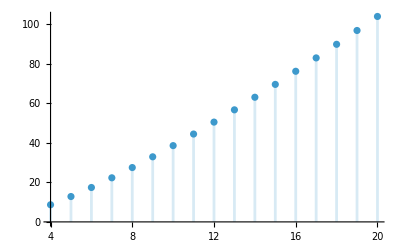

```mathematica
(* Calculating the mean in as simple of a formula as possible, for each statistic represented by clade-number basis *)
(* Sackin index *)
sackin[n_,r_] := r;
meanSackin = meanCladeStatistic[sackin, n]
DiscretePlot[meanSackin, {n, 4, 20}]
```

### Average leaf depth (A.2)

-2+2 HarmonicNumber[n]

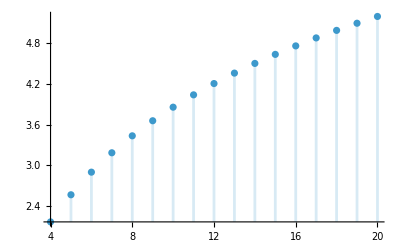

```mathematica
averageLeafDepth[n_,r_]:= r/n;
meanAverageLeafDepth = meanCladeStatistic[averageLeafDepth, n]
DiscretePlot[meanAverageLeafDepth, {n, 4, 20}]
```

### Total cophenetic index (A.4)

n (1+n-2 HarmonicNumber[n])

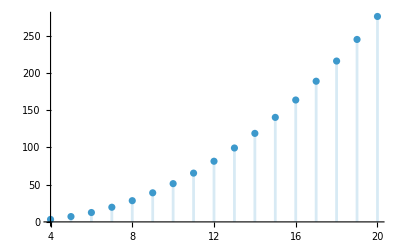

```mathematica
totalCophenetic[n_,r_]:=Piecewise[{{Binomial[r,2], r < n},{0,r == n}}];
meanTotalCophenetic = meanCladeStatistic[totalCophenetic,n]
DiscretePlot[meanTotalCophenetic, {n, 4, 20}]
```

### s-hat shape statistic (A.5)

Log[-1+n]+∑_(r=2)^(-1+n) (2 n Log[-1+r])/(r (1+r))

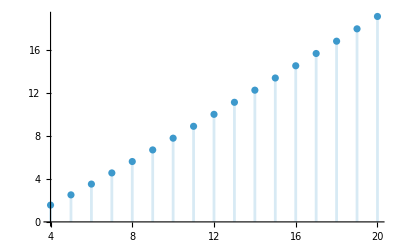

```mathematica
sHat[n_,r_] :=Log[r-1];
meanSHat = meanCladeStatistic[sHat, n]
DiscretePlot[meanSHat, {n, 4, 20}]
```

### Quadratic Colless index (A.11)

```mathematica
quadraticColless[n_,r_]:= Piecewise[{{r^2, r < n}, {2n-n^2, r==n}}];
meanQuadraticColless = meanCladeStatistic[quadraticColless, n]
DiscretePlot[meanQuadraticColless, {n, 4, 20}]
```

n (1+n-2 HarmonicNumber[n])

-Graphics-

### Total internal path length (A.21)

2-4 n+2 n HarmonicNumber[n]

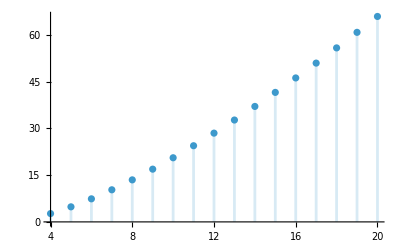

```mathematica
tIPL[n_,r_]:=Piecewise[{{r, r<n}, {2-n, r == n}}];
meanTIPL = meanCladeStatistic[tIPL, n]
DiscretePlot[meanTIPL, {n, 4, 20}]
```

### Total path length (A.22)

2-6 n+4 n HarmonicNumber[n]

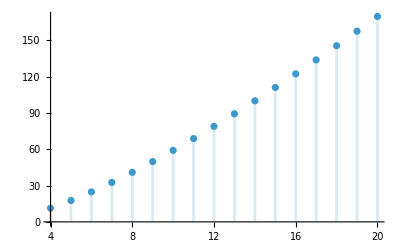

```mathematica
tPL[n_,r_]:=Piecewise[{{2r, r < n}, {2, r==n}}];
meanTPL = meanCladeStatistic[tPL, n]
DiscretePlot[meanTPL, {n, 4, 20}]
```

### Average Vertex Depth (A.23)

(2-6 n+4 n HarmonicNumber[n])/(-1+2 n)

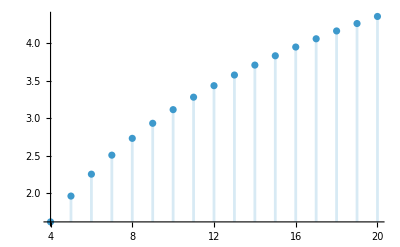

```mathematica
aVD[n_,r_]:=Piecewise[{{2r/(2n-1), r < n}, {2/(2n-1), r == n}}];meanAVD = meanCladeStatistic[aVD, n]
DiscretePlot[meanAVD, {n, 4, 20}]
```

## Balance indices represented by the daughter-number basis

Finding the mean of balance indices represented by the daughter-number basis is a bit trickier. Instead of summing over , we will first sum over all pairs  with , for r = 2, ..., n, and then sum those partial sums up. Recall that the mean of a statistic  which is represented by the daughter-number basis with coefficients  is given by (eqs. 6.2, 6.3)

The expected daughter number  now has two cases, because  unless , in which case it is equal to . Therefore, to find the internal sum for a fixed value of , if r is even it will be equal to 

while if  is odd the internal sum will be equal to 

Now, splitting into the cases where  and   and separating into  even and  odd gives us our full expressions for sums, which we do out below.

## Code for daughter-number basis

```mathematica
(* Function to solve mean for statistics represented by daughter-number basis *)
(* Sum p_k(i) * stat[n, i, j] over a level set i + j = k; split into k even and k odd *)
partialSumEvenR[stat_, n_, r_] := Sum[stat[n,i, r-i] * 2/(r-1), {i, 1, r/2 - 1}] + stat[n, r/2, r/2] /(r-1);
partialSumOddR[stat_, n_,r_]:= Sum[stat[n,i, r-i] * 2/(r-1), {i, 1, (r-1)/2 }];

(* Now sum M(n,k) * partial Sum over k=2,...,n, splitting into even and odd n cases. k0=2 is the default*)
meanStatEvenN[stat_, n_] := FullSimplify[Sum[2n/(r(r+1)) * partialSumEvenR[stat, n,r], {r, 2, n-2, 2}]
+ Sum[2n/(r(r+1))*partialSumOddR[stat, n, r], {r, 3, n-1, 2}] 
+ partialSumEvenR[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
meanStatOddN[stat_, n_] := FullSimplify[Sum[2n/(r(r+1)) * partialSumEvenR[stat, n,r], {r, 2, n-1, 2}]
+ Sum[2n/(r(r+1))*partialSumOddR[stat, n, r], {r, 3, n-2, 2}] 
+ partialSumOddR[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];

(* Aggregate into a final function *)
(* Simplify in a way that chooses a form involving HarmonicNumber instead of PolyGamma functions *)
simpHarmonic=FullSimplify[#,ComplexityFunction->(LeafCount[#]+100Count[#,_PolyGamma,All]&)]&;

meanDaughterStatistic[stat_, n_] := simpHarmonic[Piecewise[{{meanStatEvenN[stat, n], Mod[n,2] == 0}, {meanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>3,n∈Integers}];
```

```mathematica
(* Representations of indices represented by the daughter-number basis *)
colless[n_,i_,j_]:= j-i;
correctedColless[n_,i_,j_]:=2(j-i)/(n-1)/(n-2);
i2[n_,i_,j_]:=Piecewise[{{(j-i)/((n-2)(i+j-2)), i+j > 2}, {0, i+j == 2}}];
totalI[n_,i_,j_]:=(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]); (* 0 when i + j < 4; use modified function *)
totalIPrime[n_,i_,j_]:= Piecewise[{{(i+j - 1)/(i + j)*(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]), Mod[i + j, 2]== 0}, {(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]), Mod[i + j, 2] == 1}}]; (* 0 when i + j < 4; use modified function *)
rogersJ[n_,i_,j_]:=Piecewise[{{1, i != j}, {0, i == j}}];
rQIB[n_,i_,j_]:=Binomial[i,2]*Binomial[j,2];
stairs1[n_,i_,j_]:=Piecewise[{{1/(n-1), i != j}, {0, i == j}}];
stairs2[n_,i_,j_]:=i/j/(n-1);
```

### Colless index (A.8)

Piecewise[{{n (-1+HarmonicNumber[n/2]), Mod[n,2]==0}, {1-n+n HarmonicNumber[1/2 (-1+n)], Mod[n,2]==1}, {0, True}}]

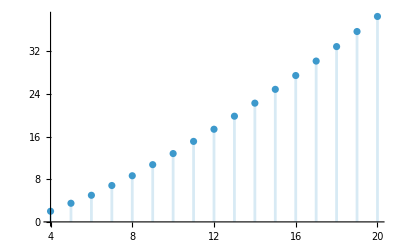

```mathematica
colless[n_,i_,j_]:= j-i;
collessmean = meanDaughterStatistic[colless, n]
DiscretePlot[collessmean, {n, 4, 20}]
```

### Corrected Colless index (A.9)

Piecewise[{{(2 n (-1+HarmonicNumber[n/2]))/((-2+n) (-1+n)), Mod[n,2]==0}, {(2 (1-n+n HarmonicNumber[1/2 (-1+n)]))/(2-3 n+n^2), Mod[n,2]==1}, {0, True}}]

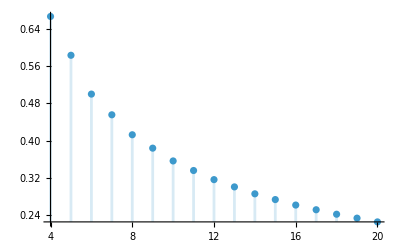

```mathematica
correctedColless[n_,i_,j_]:=2(j-i)/(n-1)/(n-2);correctedCollessmean = meanDaughterStatistic[correctedColless, n]
DiscretePlot[correctedCollessmean, {n, 4, 20}]
```

### Equal weights Colless (I2) index (A.10)

Piecewise[{{(n (6/(-1+n)+4 HarmonicNumber[1/2 (-3+n)]-4 HarmonicNumber[n/2]+Log[256]))/(12 (-2+n)), Mod[n,2]==0}, {(6 (1+n)+4 (-2+n) n (HarmonicNumber[1/2 (-4+n)]-HarmonicNumber[1/2 (-1+n)]+Log[4]))/(12 (-2+n)^2), Mod[n,2]==1}, {0, True}}]

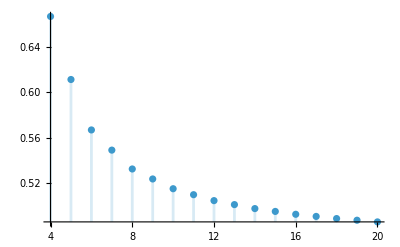

```mathematica
(*  Wrote custom functions to handle requirement that i+j>2 *)
i2[n_,i_,j_]:= (j - i) / (i + j - 2) / (n - 2);(* Only valid when i + j = k > 2 *)
meanI2EvenN[n_]:=Sum[2n/(k(k+1)) * partialSumEvenR[i2, n,k], {k, 4, n-2, 2}]+ Sum[2n/(k(k+1))*partialSumOddR[i2, n, k], {k, 3, n-1, 2}] + partialSumEvenR[i2, n, n];
meanI2OddN[n_]:=Sum[2n/(k(k+1)) * partialSumEvenR[i2, n,k], {k, 4, n-1, 2}]+ Sum[2n/(k(k+1))*partialSumOddR[i2, n, k], {k, 3, n-2, 2}] + partialSumOddR[i2, n, n];
i2meanFull[n_]:=simpHarmonic[Piecewise[{{meanI2EvenN[n], Mod[n,2]==0}, {meanI2OddN[n], Mod[n,2]==1}}],
Assumptions -> {n>3,n∈Integers}];

i2mean= i2meanFull[n]
DiscretePlot[i2mean, {n, 4, 20}]
```

```mathematica
(* Simplified this expression by hand further *)
i2meanSimplified = Piecewise[{{1/(6 (-2+n))n (4 (HarmonicNumber[n] - HarmonicNumber[n/2]) - 1/(-1+n)), Mod[n, 2] == 0}, {-1/(6 (-2+n)^2)(-3+n+4 (-2+n) n HarmonicNumber[1/2 (-1+n)]-4 (-2+n) n HarmonicNumber[-1+n]), Mod[n,2 ] == 1}}]
DiscretePlot[i2meanSimplified, {n, 4, 20}]
FullSimplify[i2mean==i2meanSimplified, Assumptions->{n>3,n∈Integers}]
```

Piecewise[{{(n (-1/(-1+n)+4 (-HarmonicNumber[n/2]+HarmonicNumber[n])))/(6 (-2+n)), Mod[n,2]==0}, {-(-3+n+4 (-2+n) n HarmonicNumber[1/2 (-1+n)]-4 (-2+n) n HarmonicNumber[-1+n])/(6 (-2+n)^2), Mod[n,2]==1}, {0, True}}]

-Graphics-

True

### Total I index (A.13)

```mathematica
totalI[n_,i_,j_]:=(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]); (* 0 when i + j < 4; use modified function *)
```

Piecewise[{{1/12 n (-5+6 HarmonicNumber[1/2 (-1+n)]-6 HarmonicNumber[n/2]+Log[4096]), Mod[n,2]==0}, {1/12 n (-5+6 HarmonicNumber[1/2 (-2+n)]-6 HarmonicNumber[1/2 (-1+n)]+Log[4096]), Mod[n,2]==1}, {0, True}}]

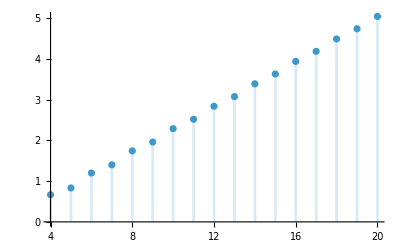

```mathematica
(* For total I / total I', we write slightly modified functions because it is 0 for k < 4 *)
modifiedmeanStatEvenN[stat_,n_] := Sum[2n/(k(k+1)) * partialSumEvenR[stat, n,k], {k, 4, n-2, 2}]+ Sum[2n/(k(k+1))*partialSumOddR[stat, n, k], {k, 5, n-1, 2}] + partialSumEvenR[stat, n, n];
modifiedmeanStatOddN[stat_, n_] := Sum[2n/(k(k+1)) * partialSumEvenR[stat, n,k], {k, 4, n-1, 2}]+ Sum[2n/(k(k+1))*partialSumOddR[stat, n, k], {k, 5, n-2, 2}] + partialSumOddR[stat, n, n];
modifiedmeanDaughterStatistic[stat_,n_]:=simpHarmonic[Piecewise[{{modifiedmeanStatEvenN[stat, n], Mod[n,2] == 0}, {modifiedmeanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>3,n∈Integers}];

totalImean = modifiedmeanDaughterStatistic[totalI, n]
DiscretePlot[totalImean, {n, 4, 20}]
```

```mathematica
(* Using the above, I simplified the formula further by hand *)totalImeanSimplified = Piecewise[{{n(HarmonicNumber[n] - HarmonicNumber[n/2] -5/12), Mod[n,2]==0}, {n(HarmonicNumber[n-1] - HarmonicNumber[(n-1)/2] -5/12) , Mod[n,2]==1}}]
DiscretePlot[totalImeanSimplified, {n, 4, 20}]
FullSimplify[totalImean ==totalImeanSimplified, Assumptions->{n>3, n∈Integers}]
```

Piecewise[{{n (-5/12-HarmonicNumber[n/2]+HarmonicNumber[n]), Mod[n,2]==0}, {n (-5/12-HarmonicNumber[1/2 (-1+n)]+HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

True

### Total I’ index (A.15)

Piecewise[{{1/4 (-2+n), (n≠3&&Mod[n,2]==1)||Mod[n,2]==0}, {3/4, Mod[n,2]==1}, {0, True}}]

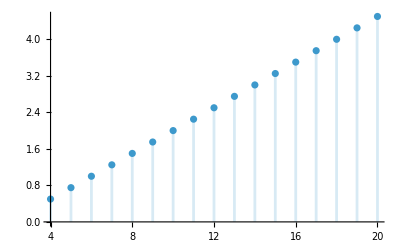

```mathematica
totalIPrime[n_,i_,j_]:= Piecewise[{{(i+j - 1)/(i + j)*(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]), Mod[i + j, 2]== 0}, {(j - Ceiling[(i+j)/2])/((i+j-1) - Ceiling[(i+j)/2]), Mod[i + j, 2] == 1}}];totalIPrimemean = modifiedmeanDaughterStatistic[totalIPrime, n]
DiscretePlot[totalIPrimemean, {n, 4, 20}]
```

```mathematica
totalIPrimeSimplest = n/4 - 1/2
FullSimplify[totalIPrimemean== totalIPrimeSimplest, Assumptions ->{n>3, n∈Integers}]
```

-1/2+n/4

True

### Rogers J index (A.17)

Piecewise[{{n (2-2/(-1+n)-HarmonicNumber[1/2 (-3+n)]+HarmonicNumber[1/2 (-2+n)]-Log[4]), Mod[n,2]==0}, {-2-n HarmonicNumber[1/2 (-2+n)]+n HarmonicNumber[1/2 (-1+n)]-n (-2+Log[4]), Mod[n,2]==1}, {0, True}}]

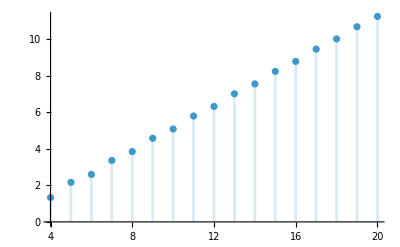

```mathematica
(* Coefficient is 1 if i \neq j and 0 if i = j *)
(* Wrote code by hand to simplify easier *)
rogersJPartialSumEvenR[n_, r_] := Simplify[Sum[1* 2/(r-1), {i, 1, r/2 - 1}],Assumptions->{n>3,n∈Integers, 2 <= r <= n, Mod[r, 2]==0}] ;
rogersJPartialSumOddR[n_,r_]:= Simplify[Sum[1* 2/(r-1), {i, 1, (r-1)/2 }], Assumptions->{n>3,n∈Integers, 2 <= r <= n, Mod[r, 2]==1}];

(* Now sum M(n,k) * partial Sum over k=2,...,n, splitting into even and odd n cases. k0=2 is the default*)
meanRogersJEvenN[ n_] := Simplify[Sum[2n/(r(r+1)) * rogersJPartialSumEvenR[ n,r], {r, 2, n-2, 2}]+ Sum[2n/(r(r+1))*rogersJPartialSumOddR[n, r], {r, 3, n-1, 2}] + rogersJPartialSumEvenR[n, n], Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
meanRogersJOddN[n_] := Simplify[Sum[2n/(r(r+1)) * rogersJPartialSumEvenR[ n,r], {r, 2, n-1, 2}]+ Sum[2n/(r(r+1))*rogersJPartialSumOddR[n, r], {r, 3, n-2, 2}] + rogersJPartialSumOddR[ n, n],Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];

rogersJMean[n_]:= simpHarmonic[Piecewise[{{meanRogersJEvenN[ n], Mod[n,2] == 0}, {meanRogersJOddN[n], Mod[n,2] == 1}}], Assumptions -> {n>3,n∈Integers}]
rogersJmeanResult = rogersJMean[n]
DiscretePlot[rogersJMean[n], {n, 4, 20}]
```

```mathematica
(* Computed simplified equation by hand using basic identities *)
rogersJmeanSimplified = Piecewise[{{2n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + 1), Mod[n,2]==0},{2n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n-1] + 1) - 2, Mod[n,2]==1}}]
DiscretePlot[rogersJmeanSimplified, {n, 4, 20}]
```

Piecewise[{{2 n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]), Mod[n,2]==0}, {-2+2 n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[rogersJmeanResult==rogersJmeanSimplified, Assumptions->{n>3, n∈Integers}]
```

True

### Rooted quartet index for binary trees (A.18)

Piecewise[{{1/72 (-3+n) (-2+n) (-1+n) n, Mod[n,2]==0||Mod[n,2]==1}, {0, True}}]

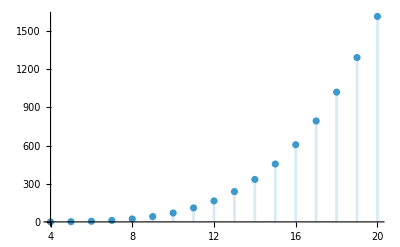

```mathematica
rQIB[n_,i_,j_]:=Binomial[i,2]*Binomial[j,2];
rQIBmean = meanDaughterStatistic[rQIB, n]
DiscretePlot[rQIBmean, {n, 4, 20}]
```

```mathematica
rQIBmeanSimplest = Binomial[n, 4] / 3
DiscretePlot[rQIBmeanSimplest, {n, 4, 20}]
FullSimplify[rQIBmean == rQIBmeanSimplest, Assumptions->{n>3, n∈Integers}]
```

1/72 (-3+n) (-2+n) (-1+n) n

-Graphics-

True

### stairs1 index (A.28). This is just the formula for Rogers J divided by n-1; see section above on Rogers J verification

### stairs2 index (A.29) Most complicated formula to simplify and show equivalence

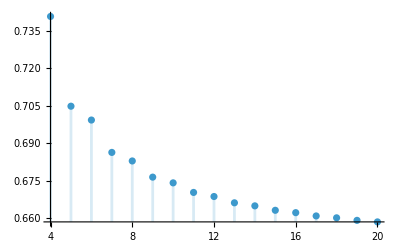

```mathematica
stairs2[n_,i_,j_]:= i / j / ( n - 1);
stairs2meanNaive[n_]:= meanDaughterStatistic[stairs2, n]
DiscretePlot[stairs2meanNaive[n], {n, 4, 20}]
```

```mathematica
stairs2meanSimplified = Piecewise[{
   {(2 n HarmonicNumber[n - 1, 2] - n HarmonicNumber[n/2, 2] - 2 (HarmonicNumber[n - 1] - HarmonicNumber[n/2]) - (n - 1))/(n - 1), Mod[n, 2] == 0},
   {(2 n HarmonicNumber[n - 1, 2] - n HarmonicNumber[(n - 1)/2, 2] - 2 (HarmonicNumber[n - 1] - HarmonicNumber[(n - 1)/2]) - (n - 1))/(n - 1), Mod[n, 2] == 1}}]
DiscretePlot[stairs2meanSimplified, {n, 4, 20}]
```

Piecewise[{{(1-n-2 (HarmonicNumber[-1+n]-HarmonicNumber[n/2])+2 n HarmonicNumber[-1+n,2]-n HarmonicNumber[n/2,2])/(-1+n), Mod[n,2]==0}, {(1-n-2 (-HarmonicNumber[1/2 (-1+n)]+HarmonicNumber[-1+n])-n HarmonicNumber[1/2 (-1+n),2]+2 n HarmonicNumber[-1+n,2])/(-1+n), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
(* Inner sums (times n - 1) for even r = 2m and odd r = 2m + 1, reindexed by l = r - i *)
stairs2InnerEven = FullSimplify[(Sum[2 (2 m - l)/l, {l, m + 1, 2 m - 1}] + 1)/(2 m - 1), Assumptions -> {m >= 1, Element[m, Integers]}]
stairs2InnerOdd = FullSimplify[Sum[2 (2 m + 1 - l)/l, {l, m + 1, 2 m}]/(2 m), Assumptions -> {m >= 1, Element[m, Integers]}]
```

(3-2 m+4 m (EulerGamma-HarmonicNumber[m]+PolyGamma[0,2 m]))/(-1+2 m)

-(m+HarmonicNumber[m]+2 m HarmonicNumber[m]+(-1-2 m) HarmonicNumber[2 m])/m

```mathematica
(* Both cases in one formula, using AlternatingHarmonicNumber[k] = HarmonicNumber[k] - HarmonicNumber[Floor[k/2]] *)
stairs2G[r_] := (2 r AlternatingHarmonicNumber[r - 1] - r + (-1)^(r + 1))/(r - 1);
FullSimplify[{stairs2InnerEven == stairs2G[2 m], stairs2InnerOdd == stairs2G[2 m + 1]}, Assumptions -> {m >= 1, Element[m, Integers]}]
```

{True,True}

```mathematica
(* (n - 1) E[stairs2] = g(n) + 2 n Sum[g(r)/(r (r + 1)), {r, 2, n - 1}]. Split g(r)/(r (r + 1)) into 2 AlternatingHarmonicNumber[r - 1]/((r - 1) (r + 1)) and a remainder; in the first part, write AlternatingHarmonicNumber[r - 1] as a sum over j and swap the order of summation *)
stairs2PartA = Sum[(-1)^(j + 1)/j Simplify[Sum[2/((r - 1) (r + 1)), {r, j + 1, n - 1}]], {j, 1, n - 2}]
stairs2PartB = Simplify[Sum[(-r + (-1)^(r + 1))/((r - 1) r (r + 1)), {r, 2, n - 1}] /. LerchPhi[-1, 1, k_] :> (-1)^(k - 1) (Log[2] - AlternatingHarmonicNumber[k - 1]), Assumptions -> {n > 3, Element[n, Integers]}]
```

-1+((1-3 n+n^2) AlternatingHarmonicNumber[-2+n])/((-1+n) n)+AlternatingHarmonicNumber[-1+n]+AlternatingHarmonicNumber[-2+n,2]

-1/(2 (-2+n) (-1+n) n)(-2-2 (-1)^n+3 n+n^2-n^3+n (2-3 n+n^2) AlternatingHarmonicNumber[-3+n]+2 n (2-3 n+n^2) AlternatingHarmonicNumber[-2+n]+2 n AlternatingHarmonicNumber[-1+n]-3 n^2 AlternatingHarmonicNumber[-1+n]+n^3 AlternatingHarmonicNumber[-1+n])

```mathematica
(* Assemble, shifting all indices to n - 1 *)
stairs2meanAlt = Collect[FullSimplify[(stairs2G[n] + 2 n (stairs2PartA + stairs2PartB) /. {
      AlternatingHarmonicNumber[n] -> AlternatingHarmonicNumber[n - 1] - (-1)^n/n,
      AlternatingHarmonicNumber[n - 2] -> AlternatingHarmonicNumber[n - 1] - (-1)^n/(n - 1),
      AlternatingHarmonicNumber[n - 3] -> AlternatingHarmonicNumber[n - 1] - (-1)^n/(n - 1) + (-1)^n/(n - 2),
      AlternatingHarmonicNumber[n - 2, 2] -> AlternatingHarmonicNumber[n - 1, 2] - (-1)^n/(n - 1)^2}),
    Assumptions -> {n > 3, Element[n, Integers]}], AlternatingHarmonicNumber[__]]/(n - 1)
```

(1-n-2 AlternatingHarmonicNumber[-1+n]+2 n AlternatingHarmonicNumber[-1+n,2])/(-1+n)

```mathematica
(* Convert back with AlternatingHarmonicNumber[k, s] = HarmonicNumber[k, s] - 2^(1 - s) HarmonicNumber[Floor[k/2], s] *)
stairs2mean = stairs2meanAlt /. AlternatingHarmonicNumber[k_, s_ : 1] :> HarmonicNumber[k, s] - 2^(1 - s) HarmonicNumber[Floor[k/2], s]
```

1/(-1+n)(1-n-2 (HarmonicNumber[-1+n]-HarmonicNumber[Floor[1/2 (-1+n)]])+2 n (HarmonicNumber[-1+n,2]-1/2 HarmonicNumber[Floor[1/2 (-1+n)],2]))

```mathematica
(* Check for n = 2m and n = 2m + 1, shifting harmonic numbers to arguments m and 2m via HarmonicNumber[x + a, s] = HarmonicNumber[x, s] + finite sum. (FullSimplify here can crash the Mathematica 15.0 kernel.) *)
hShift = HarmonicNumber[x_ + a_Integer, s_ : 1] :> HarmonicNumber[x, s] + If[a > 0, Sum[1/(x + i)^s, {i, 1, a}], -Sum[1/(x + i)^s, {i, a + 1, 0}]];
Simplify[Simplify[{stairs2mean - stairs2meanSimplified /. n -> 2 m, stairs2mean - stairs2meanSimplified /. n -> 2 m + 1}, Assumptions -> {m >= 2, Element[m, Integers]}] /. hShift, Assumptions -> {m >= 2, Element[m, Integers]}]
```

{0,0}

```mathematica
(* Everything simplifies correctly to verify the formula *)
```